```mathematica
(*w=1*)
q[v_]:=0.5*Erfc[v/(√2)];
(*Int*)
gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w(k+b-(1-beta/ns)w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=k+b-(1-beta/ns)w x;
(*gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w(k+b-w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=k+b-w x;*)
g1Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[gTmp1[x, b, k, beta, ns, w] Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g21Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[gTmp2[x, b, k, beta, ns, w]^2 Exp[-x^2/2.]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g22Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(gTmp1[x, b, k, beta, ns, w]^2-gTmp2[x, b, k, beta, ns, w]^2/w^2) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g31Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[3gTmp1[x, b, k, beta, ns, w] gTmp2[x, b, k, beta, ns, w]^2 Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g32Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(gTmp1[x, b, k, beta, ns, w]^3-(3gTmp1[x, b, k, beta, ns, w] gTmp2[x, b, k, beta, ns, w]^2)/w^2) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
betaSolution[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21Int[b, k, nd, ns, ndR, y, w]-2g1Int[b, k, nd, ns, ndR, y, w]+g22Int[b, k, nd, ns, ndR, y, w]/ns , {y, 0.0, 100.}, Method->"Brent"];
getSkewNormalParam[ns_,  beta_, gsList_, u0_, t_]:=Module[{g1, g21, g31, g32, m1, m2, m3, tmp, mu, sigma, alpha}, 
{g1, g21, g31, g32}=gsList;
m1 = u0 Exp[-g1 t/ns];
m2 = 1.+(u0^2 -1)Exp[-g21 t/ns];
m3=(3.g21-g31/ns)/(3g21-4g1+g32/ns^2)u0 Exp[-g1 t/ns]+(u0^3-(3.g21-g31/ns)/(3g21-4g1+g32/ns^2)u0)Exp[-(3g21-3g1+g32/ns^2)/ns t];
tmp=Sign[m3-3m1 m2 +2 m1^3] √(π/2.)(Abs[2/(4-π)(m3-3m1 m2 +2 m1^3)])^(1/3);
mu=m1-√(2./π) tmp;
sigma =√(m2-m1^2+2./π tmp^2);
alpha = √(tmp^2/(sigma^2-tmp^2))Sign[tmp];
{mu, sigma, alpha}

];
getNormalParam[ns_,  beta_, gsList_, u0_, t_]:=Module[{g1, g21, g31, g32, m1, m2, mu, sigma}, 
{g1, g21, g31, g32}=gsList;
m1 = u0 Exp[-g1 t/ns];
m2 = 1.+(u0^2 -1)Exp[-g21 t/ns];
mu=m1;
sigma=√(m2-m1^2);
{mu, sigma}
];

puu0SkewNormal[u_, u0_, t_, ns_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
PDF[SkewNormalDistribution[mu, sigma, alpha], u]
];
puu0Normal[u_, u0_, t_, ns_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
PDF[NormalDistribution[mu, sigma], u]
];
```

10.0242

{4.20363,0.849074,-1.08055}

{3.70641,0.688264}

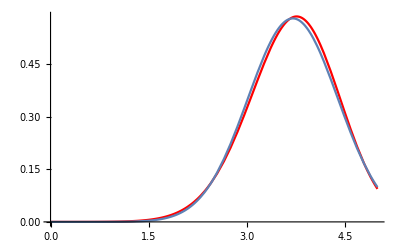

```mathematica
b=2.75;k=2.25;nd=200;ns=300;ndR=4;
beta=betaSolution[b, k, nd, ns, ndR, 1.]//Quiet
(*getSkewNormalParam[b, k, nd, ndR, ns, beta, 1., b+k, 5000]*)
gsList = {g1Int[b, k, nd, ns, ndR, beta, 1.], g21Int[b, k, nd, ns, ndR, beta, 1.],g31Int[b, k, nd, ns, ndR, beta, 1.],g32Int[b, k, nd, ns, ndR, beta, 1.]};
getSkewNormalParam[ns, beta, gsList, b+k, 1200]
getNormalParam[ns, beta, gsList, b+k, 1200]
Show[Plot[puu0SkewNormal[u, b+k, 1200, ns, beta, gsList], {u, 0, 5}, PlotRange->All, PlotStyle->Red],
Plot[puu0Normal[u, b+k, 1200, ns, beta, gsList], {u, 0, 5}, PlotRange->All]]
```

```mathematica
tmpList = Table[{u, puu0SkewNormal[u, b+k, 1200, ns, beta, gsList]}, {u, 1, 8, 0.1}];
Export["tmpList.csv",tmpList,"CSV"];
```

```mathematica
(***************************************************************************************************************************)
(*z=ReLU(u-b)*)
(*expectation value of z with initial overlap u0*)
expzu0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b), {u, b, Infinity}]
];

expzu0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
(ⅇ^((-(b- mu)^2)/(2 sigma^2))sigma)/(√(2. π))-0.5(b-mu) Erfc[(b-mu)/(√2. sigma)]
];
(*expectation value of z^2 with initial overlap u0*)
expz2u0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b)^2, {u, b, Infinity}]
];
expz2u0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
(ⅇ^((-(b-mu)^2)/(2 sigma^2)) sigma(-b+mu))/(√(2. π))+0.5 (sigma^2+(b-mu)^2) Erfc[(b-mu)/(√2. sigma)]
];
(*The probability that z is 0*)
au0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha},
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u], {u, -Infinity, b}]
];
au0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
 0.5+0.5*Erf[(b-mu)/(√2. sigma)]
];
(*expectation value of z^3 with initial overlap u0*)
expz3u0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b)^3, {u, b, Infinity}]
];
expz3u0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
(ⅇ^(-(b-mu)^2/(2 sigma^2)) ((b-mu)^2 sigma+2 sigma^3))/(√(2. π))-0.5 (b-mu) ((b-mu)^2+3 sigma^2) Erfc[(b-mu)/(√2 sigma)]
];
(*expectation value of z^4 with initial overlap u0*)
expz4u0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b)^4, {u, b, Infinity}]
];
expz4u0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
(ⅇ^(-(b-mu)^2/(2 sigma^2)) (-(b-mu)^3 sigma+5 (-b+mu) sigma^3))/(√(2. π))+1/2. ((b-mu)^4+6 (b-mu)^2 sigma^2+3 sigma^4) Erfc[(b-mu)/(√2 sigma)]
];
(*---------------------Part I begins-----------------------------------*)
(*Part I: For the group of dendrites that are not picked for update at time 0.*)
(*the dendrite with overlap v is picked for update*)
pLeftMarginI[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^(Rnd-1) qv/(1-qv)*(nd-m)/(Rnd -m));(*qv should always be q[v]*)
(*although the distribution of u is a skew gaussian, the distribution of YI is still assumed to be a delta function at 0 + the positive part of a gaussian*)
getYIParams[t_, b_, k_, ns_,nd_, ndR_, beta_, gsList_]:=Module[{expzI, expz2I, aI, expYI, expY2I, AI, muOverSigmaYI, sigmaYI, muYI}, 
(*expzI = NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0SkewNormal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];*)
expzI =NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0Normal[u0, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, -5(b+k), v}];
(*expz2I:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0SkewNormal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];*)
expz2I=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0Normal[u0, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, -5(b+k), v}];
(*aI = NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) au0SkewNormal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];*)
aI = NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) au0Normal[u0, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, -5(b+k), v}];
(*--------------------------------------------------------*)
expYI=(nd-ndR)expzI;
expY2I=(nd-ndR)(nd-ndR-1)expzI^2 + (nd-ndR)expz2I;
AI=aI^(nd-ndR);
(*--------------------------------------------------------*)
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
muOverSigmaYI = x/.FindRoot[((1-AI)expY2I)/expYI^2 h[x]^2==1+x h[x], {x, 100.}];
sigmaYI=expYI/((1-AI)h[muOverSigmaYI]);
muYI=muOverSigmaYI*sigmaYI;
{muYI, sigmaYI, AI}

];
(*---------------------Part I ends-----------------------------------*)
(*Get the 1% false positive boundary. At steady state, the distribution of u should be a standard gaussian distribution. *)
getThreshold[b_, nd_]:=Module[{expz, expz2, a, expY, expY2, A, muOverSigmaSteady, muSteady, sigmaSteady},
expz=(ⅇ^(-b^2/2))/(√(2. π))-0.5 b Erfc[b/(√2.)];
expz2=-(b ⅇ^(-b^2/2))/(√(2.π))+0.5 (1+b^2) Erfc[b/(√2.)];
a=0.5 (1+Erf[b/(√2)]);
expY=nd expz;
expY2=nd(nd-1)expz^2 + nd expz2;
A=a^nd;
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
muOverSigmaSteady= x/.FindRoot[((1-A)expY2)/expY^2 h[x]^2==1+x h[x], {x, 100.}]//Quiet;
sigmaSteady=expY/((1-A)h[muOverSigmaSteady]);
muSteady=muOverSigmaSteady*sigmaSteady;
muSteady-√2 sigmaSteady InverseErf[(0.01(1+Erf[muSteady/(√2 sigmaSteady)]))/(1-A)-1]//Quiet
 ];
(*---------------------Part II begins-----------------------------------*)
(*Part II: For the group of dendrites that are picked for update at time 0.*)
(*the dendrite with overlap v is not picked for update*)
pLeftMarginII[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));(*qv should always be q[v]*)
(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
funErf[x_]:=0.5*(1+Erf[x/(√2)]);
funExp[x_]:=Exp[-x^2/2]/(√(2π));
c0[x_]:=funErf[x];
c1[x_]:=funExp[x]+funErf[x] x;
c2 [x_]:=funExp[x] x + funErf[x](1+x^2);
c3 [x_]:=funExp[x](2+x^2) + funErf[x](3x+x^3);
c4 [x_]:=funExp[x](5x+x^3)+funErf[x](3+6 x^2+x^4);
c5[x_]:=funExp[x](x^2+1)(x^2+8)+funErf[x](15x+10 x^3+x^5);
anumFun[x_, m1_, m2_, m3_]:=(m2 c1[x]^3 ((m1 m2-m3) c3[x]-m1 m2 c4[x])+c1[x]^2 ((-m1^2+m2) m3 c2[x]^2+(m1^2+m2) m3 c2[x] c3[x]+m1 m2^2 c0[x] c4[x])+m1 c0[x] (m1 m3 c2[x]^3+(m2^2-m1 m3) c2[x]^2 c3[x]+m1^2 m2 c0[x] c3[x]^2-m1^2 m2 c0[x] c2[x] c4[x])-m2 c1[x] (m3 c2[x]^3+m1^3 c0[x] c3[x]^2+m1 c0[x] c2[x] (2 m2 c3[x]-m1^2 c4[x])));
adenFun[x_, m1_, m2_, m3_]:=(m2 m3 c2[x]^4+m2 c1[x]^3 ((m1 m2-m3) c3[x]-2 m1 m2 c4[x])+m1^3 m2 c0[x]^2 (c3[x]^2-c2[x] c4[x])-m2 c1[x] (2 m3 c2[x]^3+(m1 m2+m3) c2[x]^2 c3[x]+2 m1^3 c0[x] c3[x]^2+2 m1 c0[x] c2[x] (m2 c3[x]-m1^2 c4[x]))+m1 c0[x] c2[x] (m1 m3 c2[x]^2+m1 m3 c3[x]^2+c2[x] (2 (m2^2-m1 m3) c3[x]-m2^2 c4[x]))+c1[x]^2 ((-m1^2+m2) m3 c2[x]^2+c2[x] (2 (m1^2+m2) m3 c3[x]-m1 (m1^2-2 m2) m2 c4[x])+m1 (m1 (m1 m2-m3) c3[x]^2+m2^2 c0[x] c4[x])));
funTmp[x_, m1_, m2_, m3_]:=m2 ((adenFun[x, m1, m2, m3]-anumFun[x, m1, m2, m3])c1[x]+anumFun[x, m1, m2, m3] c2[x])^2-m1^2 ((adenFun[x, m1, m2, m3]-anumFun[x, m1, m2, m3])c2[x]+anumFun[x, m1, m2, m3] c3[x])((adenFun[x, m1, m2, m3]-anumFun[x, m1, m2, m3])c0[x]+anumFun[x, m1, m2, m3] c1[x]);
(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)

getYIIParams[t_, b_, k_, ns_,nd_, ndR_, beta_, gsList_]:=Module[{aII, expzII, expz2II, expz3II, expz4II, AII, expYII, expY2II, expY3II, expY4II,  xList, aList, sigmaList, m4List, idx, muOverSigmaYII, muYII, sigmaYII, aYII}, 
(*the simple but less accurate version, (not considering the possibility that a dendrite is picked for update but not updated because its overlap is already above b+k)*)
(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
expzII = expzu0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expzII = expzu0Normal[b+k, t, ns, b, beta, gsList];*)
expz2II = expz2u0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expz2II = expz2u0Normal[b+k, t, ns, b, beta, gsList];*)
expz3II = expz3u0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expz3II = expz3u0Normal[b+k, t, ns, b, beta, gsList];*)
expz4II = expz4u0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expz4II = expz4u0Normal[b+k, t, ns, b, beta, gsList];*)
aII = au0SkewNormal[b+k, t, ns, b, beta, gsList];
(*aII = au0Normal[b+k, t, ns, b, beta, gsList];*)
(*the complex but more accurate version*)
(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
(*expzII = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expzu0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expzII =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expzu0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)
expz2II =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz2u0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz2u0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expz2II = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz2u0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz2u0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)
expz3II =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz3u0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz3u0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expz3II = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz3u0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz3u0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)
expz4II =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz4u0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz4u0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expz4II = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz4u0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz4u0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)*)

(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
expYII = ndR expzII;
expY2II =  ndR expz2II+ndR(ndR-1)expzII^2;
expY3II = ndR expz3II + 3ndR(ndR-1)expzII expz2II +ndR(ndR-1)(ndR-2)expzII^3;
expY4II=ndR expz4II +ndR(ndR-1)(4expzII expz3II + 3 expz2II^2)+6ndR(ndR-1)(ndR-2)expzII^2 expz2II+ndR(ndR-1)(ndR-2)(ndR-3)expzII^4;
AII = aII^ndR;
(*--------------------------------------------------------*)
(*muOverSigmaYII=x/. FindRoot[funTmp[x, expYII, expY2II, expY3II]==0, {x, 9.,0.,  10.}]//Quiet;*)
xList=Table[x/.FindRoot[funTmp[x, expYII/(1-AII), expY2II/(1-AII), expY3II/(1-AII)]==0, {x, i, -2, 10}], {i, -2, 10, 0.2}]//Quiet;
aList=anumFun[xList, expYII/(1-AII), expY2II/(1-AII), expY3II/(1-AII)]/adenFun[xList,expYII/(1-AII), expY2II/(1-AII), expY3II/(1-AII)];
sigmaList=expYII/(1-AII) *(c0[xList](1-aList)+aList c1[xList])/(c1[xList](1-aList)+aList c2[xList]);
m4List = sigmaList^4(c4[xList](1-aList)+aList c5[xList])/(c0[xList](1-aList)+aList c1[xList]);
idx=FirstPosition[(m4List-expY4II/(1-AII))^2, Min[(m4List-expY4II/(1-AII))^2]][[1]];
muOverSigmaYII=xList[[idx]];
aYII=aList[[idx]];
sigmaYII=sigmaList[[idx]];
(*aYII=anumFun[muOverSigmaYII, expYII, expY2II, expY3II]/adenFun[muOverSigmaYII, expYII, expY2II, expY3II];
sigmaYII = expYII *(c0[muOverSigmaYII](1-aYII)+aYII c1[muOverSigmaYII])/(c1[muOverSigmaYII](1-aYII)+aYII c2[muOverSigmaYII]);*)
muYII=sigmaYII*muOverSigmaYII;
{muYII, sigmaYII, AII, aYII}
];
(*---------------------Part II ends-----------------------------------*)
probY[Y_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_, aYII_]:=Module[{xI, xII, factor1, factor2, factor3, xTmp,yTmp, tmp1, tmp2, tmp3, coef0, coef1}, 
xI = muI/sigmaI;xII=muII/sigmaII;
tmp1 = ((1-AI)AII)/c0[xI] Exp[-1/2(Y/sigmaI-xI)^2]/(√(2π)sigmaI)HeavisideTheta[Y];
tmp2= ((1-AII)AI)/(c0[xII]+aYII/(1-aYII)c1[xII])Exp[-1/2(Y/sigmaII-xII)^2]/(√(2π)sigmaII)(1+aYII/(1-aYII)(Y/sigmaII))HeavisideTheta[Y];
factor1=((1-AI)(1-AII))/(c0[xI](c0[xII]+aYII/(1-aYII) c1[xII]));
factor2=(ⅇ^(-(sigmaI xI+sigmaII xII-Y)^2/(2 (sigmaI^2+sigmaII^2))))/(√(2 π) √(sigmaI^2+sigmaII^2));
factor3 = sigmaI/(√(sigmaI^2+sigmaII^2));
coef0 = 1;coef1=aYII/(1-aYII)*factor3;
xTmp=(sigmaI xII - sigmaII xI +Y sigmaII/sigmaI)/(√(sigmaI^2+sigmaII^2));
yTmp=(Y √(sigmaI^2+sigmaII^2))/(sigmaI sigmaII);
tmp3=factor1 factor2 ((ⅇ^(-xTmp^2/2) coef1)/(√(2 π))-(ⅇ^(-1/2 (xTmp-yTmp)^2) coef1)/(√(2 π))+1/2 (coef0+coef1 xTmp)( Erf[xTmp/(√2)]+Erf[(-xTmp+yTmp)/(√2)]))HeavisideTheta[Y];
AI AII DiracDelta[Y]+tmp1+tmp2+tmp3
];
getFalseNegative[nd_, ns_, b_, k_, ndR_, th_, beta_, gsList_, t_]:=Module[{yIParams, yIIParams}, 
yIParams=getYIParams[t, b, k, ns,nd, ndR, beta, gsList];
yIIParams=getYIIParams[t, b, k, ns,nd, ndR, beta, gsList];
1-NIntegrate[probY[Y, yIParams[[1]], yIParams[[2]], yIParams[[3]], yIIParams[[1]], yIIParams[[2]], yIIParams[[3]], yIIParams[[4]]], {Y, th, Infinity}]
];
getCapacity[nd_, ns_, b_, k_, ndR_, tStart_, tEnd_, tPrecision_]:=Module[{th, beta, gsList, t1, t2, t3, fn1, fn2, fn3},
th=getThreshold[b, nd];
beta=betaSolution[b, k, nd, ns, ndR, 1.]//Quiet;
gsList = {g1Int[b, k, nd, ns, ndR, beta, 1.], g21Int[b, k, nd, ns, ndR, beta, 1.],g31Int[b, k, nd, ns, ndR, beta, 1.],g32Int[b, k, nd, ns, ndR, beta, 1.]};
t1 = tStart;
t2 = tEnd;
t3=(t1+t2)/2.;
fn1=getFalseNegative[nd, ns, b, k, ndR, th, beta, gsList, t1]//Quiet;
fn2=getFalseNegative[nd, ns, b, k, ndR, th, beta, gsList, t2]//Quiet;
fn3=getFalseNegative[nd, ns, b, k, ndR, th, beta, gsList, t3]//Quiet;
While[t2-t1>tPrecision, 
If[fn3>0.01, 
t2=t3;fn2=fn3;,
t1=t3;fn1=fn3;];
t3=(t1+t2)/2.;
fn3=getFalseNegative[nd, ns, b, k, ndR, th, beta, gsList, t3]//Quiet;
];
t3
];
falseNegative[th_, muI_, sigmaI_, AI_, muII_, sigmaII_,AII_, aYII_]:=1-NIntegrate[probY[Y, muI, sigmaI, AI, muII, sigmaII, AII, aYII], {Y, th, Infinity}];
Y99Lower[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_,  aYII_]:=If[AI AII >=0.01, 0., th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, AII,aYII]==0.01, {th, -5(b+k), 5(b+k)}, Method->"Brent"]];
Y99Upper[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_,  aYII_]:=th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, AII, aYII]==0.99, {th, 0, 5*(b+k)}, Method->"Brent"];
YMean[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_,  aYII_]:=NIntegrate[probY[Y, muI, sigmaI, AI, muII, sigmaII, AII, aYII] Y, {Y, 0.00000001, Infinity}];
(***************************************************************************************************************************)
```

```mathematica
getCapacity[nd, ns, b, 2., ndR, 300, 1700, 1]
```

1323.68

```mathematica
b=2.25;k=1.65;nd=200;ns=300;ndR=4;
beta=betaSolution[b, k, nd, ns, ndR, 1.]//Quiet;
gsList = {g1Int[b, k, nd, ns, ndR, beta, 1.], g21Int[b, k, nd, ns, ndR, beta, 1.],g31Int[b, k, nd, ns, ndR, beta, 1.],g32Int[b, k, nd, ns, ndR, beta, 1.]};
th = getThreshold[b, nd];
Print["beta: ", beta]
Print["th: ", th]
```

beta: 4.88203

th: 3.03059

```mathematica
ndList={400}; bList={2.5, 2.75, 3.0};kList={2.0, 2.25, 2.5, 2.75, 3.0};ndRList={2, 3, 4};
paramList = Table[{nd, 60000/nd, b, k, ndR}, {nd, ndList}, {b, bList}, {k, kList}, {ndR, ndRList}];
paramList = ArrayReshape[paramList, {Length[ndList]*Length[bList]*Length[kList]*Length[ndRList],5}];
tmpFun[nd_, ns_, b_, k_, ndR_]:={nd, ns, b, k, ndR, betaSolution[b, k, nd, ns, ndR, 1.]}
betaList = MapThread[tmpFun, Transpose[paramList]]//Quiet;
```

```mathematica
Export["beta_list.txt", betaList,"Table","FieldSeparators"->" " ]
```

```mathematica
tStart=500; tEnd=1500;tStep=100;
tList=Table[t, {t, tStart, tEnd, tStep}];
yIParamsList=Table[getYIParams[t, b, k, ns, nd, ndR, beta, gsList], {t, tList}]//Quiet;
yIIParamsList = Table[getYIIParams[t, b, k, ns, nd, ndR, beta, gsList], {t, tList}]//Quiet;
fnList = Table[falseNegative[th, yIParamsList[[i, 1]], yIParamsList[[i, 2]], yIParamsList[[i, 3]], yIIParamsList[[i, 1]], yIIParamsList[[i, 2]], yIIParamsList[[i, 3]], yIIParamsList[[i, 4]]], {i, 1, Length[tList]}];//Quiet
Y99LowerList = Table[Y99Lower[yIParamsList[[i, 1]], yIParamsList[[i, 2]], yIParamsList[[i, 3]], yIIParamsList[[i, 1]], yIIParamsList[[i, 2]], yIIParamsList[[i, 3]], yIIParamsList[[i, 4]]], {i, 1, Length[tList]}];//Quiet
Y99UpperList = Table[Y99Upper[yIParamsList[[i, 1]], yIParamsList[[i, 2]], yIParamsList[[i, 3]], yIIParamsList[[i, 1]], yIIParamsList[[i, 2]], yIIParamsList[[i, 3]], yIIParamsList[[i, 4]]], {i, 1, Length[tList]}];//Quiet
YMeanList = Table[YMean[yIParamsList[[i, 1]], yIParamsList[[i, 2]], yIParamsList[[i, 3]], yIIParamsList[[i, 1]], yIIParamsList[[i, 2]], yIIParamsList[[i, 3]], yIIParamsList[[i, 4]]], {i, 1, Length[tList]}];//Quiet
```

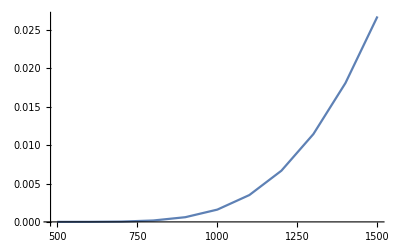

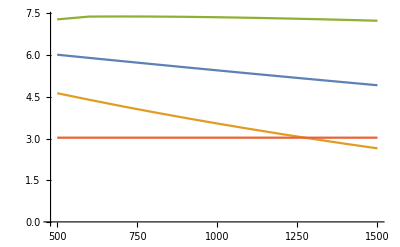

```mathematica
fnTimeList=Transpose[{tList, fnList}];
meanTimeList=Transpose[{tList, YMeanList}];
lower99TimeList= Transpose[{tList, Y99LowerList}];
upper99TimeList=Transpose[{tList, Y99UpperList}];
ListLinePlot[fnTimeList, PlotRange->All]
ListLinePlot[{meanTimeList, lower99TimeList,upper99TimeList, Table[{t, th}, {t, tList}]}, PlotRange->All]
```

```mathematica
Export["meanTimeList.txt",meanTimeList,"CSV"];
Export["lower99TimeList.csv",lower99TimeList,"CSV"];
Export["upper99TimeList.csv",upper99TimeList,"CSV"];
```

```mathematica
ns=1500;nd=40;
getCapacityVectorized[b_, k_, ndR_]:=Quiet[{b, k, ndR, TimeConstrained[getCapacity[nd, ns, b, k, ndR, 400, 1700, 1],90, -1]}];
paramList=ArrayReshape[Table[{b, k, ndR}, {b, 1.5-0.75, 1.5+0.75, 0.25}, {k, 2.25-0.75, 2.25+0.75, 0.25}, {ndR, 5, 5, 1}], {7*7*1, 3}];
```

```mathematica
capacityListTmp =Parallelize[MapThread[getCapacityVectorized, Transpose[paramList]]];
```

```mathematica
file=OpenAppend[ToString[StringForm["params_capacity_list_``_``.csv", ns, nd]]];
Export[file, capacityListTmp, "CSV"];
Close[ToString[StringForm["params_capacity_list_``_``.csv", ns, nd]]];
```

```mathematica
capacityList=Import[ToString[StringForm["params_capacity_list_``_``.csv", ns,nd]]];
(*capacityList=Import[ToString[StringForm["params_capacity_list_``_``.csv", 300,200]]];*)
```

```mathematica
ListPointPlot3D[capacityListTmp[[;;, {1, 2, 4}]]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[tmplist[[;;, {1, 2, 4}]], {tmplist, GatherBy[capacityList, #[[3]]&]}]]
```

-Graphics3D-

```mathematica
MaximalBy[GatherBy[capacityList, #[[3]]&][[1]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[2]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[3]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[4]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[5]], #[[4]]&]
```

{{3.25,2.5,1,1609.55}}

{{2.25,2.5,2,1431.81}}

{{1.75,2.5,3,1360.08}}

{{1.75,2.25,4,1315.65}}

{{1.5,2.,5,1295.97}}

```mathematica
MaximalBy[GatherBy[capacityList, #[[3]]&][[1]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[2]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[3]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[4]], #[[4]]&]
MaximalBy[GatherBy[capacityList, #[[3]]&][[5]], #[[4]]&]
```

{{3.25,2.5,1,1603.83}}

{{2.25,2.5,2,1440.06},{2.25,2.75,2,1440.06}}

{{2.,2.25,3,1374.05}}

{{1.75,2.25,4,1332.79}}

{{1.5,2.25,5,1301.68}}

```mathematica
PDF[SkewNormalDistribution[mu, sigma, alpha], x]
```

(ⅇ^(-(-mu+x)^2/(2 sigma^2)) Erfc[-(alpha (-mu+x))/(√2 sigma)])/(√(2 π) sigma)